## Execute everything here

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
dat1=Import["data/finite_persistence/scatterTn0.21Tp0.12width0.3persistence200..mx"];
dat2=Import["data/finite_persistence/scatterTn0.33Tp0.12width0.3persistence200..mx"];
dat3=Import["data/finite_persistence/scatterTn0.36Tp0.12width0.3persistence200..mx"];
dat4=Import["data/finite_persistence/scatterTn0.69Tp0.12width0.3persistence200..mx"];
dat5=Import["data/finite_persistence/scatterTn0.72Tp0.12width0.3persistence200..mx"];
dat6=Import["data/finite_persistence/scatterTn0.75Tp0.12width0.3persistence200..mx"];
```

```mathematica
idat1=Import["data/infinite_persistence/scatterTn0.21Tp0.12width0.3.mx"];
idat2=Import["data/infinite_persistence/scatterTn0.33Tp0.12width0.3.mx"];
idat3=Import["data/infinite_persistence/scatterTn0.36Tp0.12width0.3.mx"];
idat4=Import["data/infinite_persistence/scatterTn0.69Tp0.12width0.3.mx"];
idat5=Import["data/infinite_persistence/scatterTn0.72Tp0.12width0.3.mx"];
idat6=Import["data/infinite_persistence/scatterTn0.75Tp0.12width0.3.mx"];
```

```mathematica
tns={0.21,0.33,0.36,0.69,0.72,0.75};
α=tns/0.12;
```

```mathematica
dat={dat1,dat2,dat3,dat4,dat5, dat6};
idat={idat1,idat2,idat3,idat4,idat5,idat6};
```

```mathematica
Table[AppendTo[dat,idat[[i]]];,{i,Length@idat}];
```

```mathematica
Dimensions@dat
```

{12,10000,2}

```mathematica
len=Length@dat;
```

```mathematica
Length@dat
```

12

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
dθ=0.05;
temp=Table[Append[Table[FirstPosition[dat[[i,;;,1]],_?(#>θ&)],{θ,0.0,1-dθ,dθ}]//Flatten,Length@dat[[i]]],{i,1,len}];
meanscatter=Table[Table[Mean[dat[[l,temp[[l,i]];;temp[[l,i+1]]]]],{i,1,Length@temp[[l]]-1}],{l,1,len}];
varscatter=Table[Table[Variance[dat[[l,temp[[l,i]];;temp[[l,i+1]]]]],{i,1,Length@temp[[l]]-1}],{l,1,len}];
```

```mathematica
meanscatterdatwiderror=Table[Table[{meanscatter[[l,i]],ErrorBar[Sqrt@varscatter[[l,i,2]]]},{i,1,Length@meanscatter[[l]]}],{l,1,len}];
```

```mathematica
meanvars=Table[Mean[varscatter[[l,;;,2]]],{l,1,len}];
```

```mathematica
meanscatterUpper=meanscatterLower=meanscatter;
meanscatterUpper[[;;,;;,2]]+=Sqrt@varscatter[[;;,;;,2]];
meanscatterLower[[;;,;;,2]]-=Sqrt@varscatter[[;;,;;,2]];
```

## Plotting the collision statistics

{2.75,6.25}

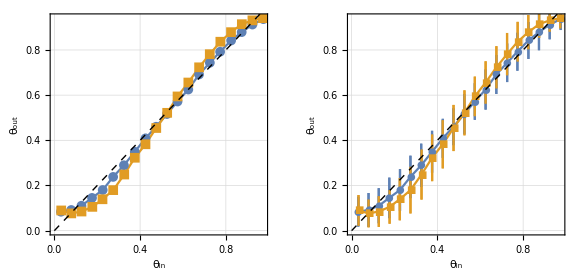

```mathematica
idx1=2;idx2=6;
{α[[idx1]],α[[idx2]]}
GraphicsRow[{Show[{ListLinePlot[meanscatter[[{idx1,idx2}]],AspectRatio->1,Frame->True,GridLines->Automatic,PlotMarkers->{Automatic, 10},FrameLabel->{"θ_in","θ_out"}],Plot[x,{x,0,1},PlotStyle->{Black,Thick,Dashed}]}],Show[{ErrorListPlot[meanscatterdatwiderror[[{idx1,idx2}]],AspectRatio->1,Frame->True,GridLines->Automatic,Joined->True,PlotMarkers->{Automatic, 10},FrameLabel->{"θ_in","θ_out"}],Plot[x,{x,0,1},PlotStyle->{Black,Thick,Dashed}]}]},ImageSize->Large]
```

comparison of α=2.75 (yellow) and α=6.25 (blue) at persistence length = 200. Note that in units of filament lengths, 200 = 31.75L. θ_in, θ_out in units rad/2.

{2.75,6.25}

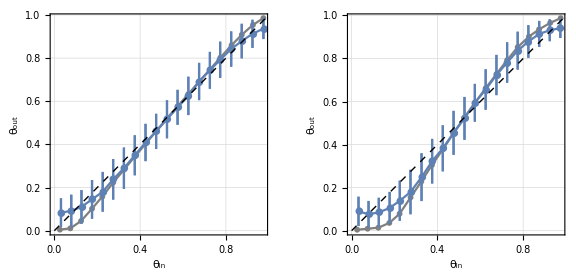

```mathematica
idx1=2;idx2=6;
{α[[idx1]],α[[idx2]]}
GraphicsRow[{Show[{ListLinePlot[meanscatter[[idx1+6]],AspectRatio->1,Frame->True,GridLines->Automatic,PlotStyle->Gray,PlotMarkers->{Automatic, 6},FrameLabel->{"θ_in","θ_out"}],ErrorListPlot[meanscatterdatwiderror[[idx1]],AspectRatio->1,Frame->True,GridLines->Automatic,Joined->True,PlotMarkers->{Automatic, 10}],Plot[x,{x,0,1},PlotStyle->{Black,Thick,Dashed}]}],Show[{ListLinePlot[meanscatter[[idx2+6]],AspectRatio->1,Frame->True,GridLines->Automatic,GridLines->Automatic,PlotStyle->Gray,PlotMarkers->{Automatic, 6},FrameLabel->{"θ_in","θ_out"}],ErrorListPlot[meanscatterdatwiderror[[idx2]],AspectRatio->1,Frame->True,GridLines->Automatic,Joined->True,PlotMarkers->{Automatic, 10}],Plot[x,{x,0,1},PlotStyle->{Black,Thick,Dashed}]}]},ImageSize->Large]
```

comparison of α=2.75 (blue, left) and α=6.25 (blue, right) at persistence length = 200, to the corresponding curves with L_p= ∞ (gray lines).  θ_in, θ_out in units rad/2.

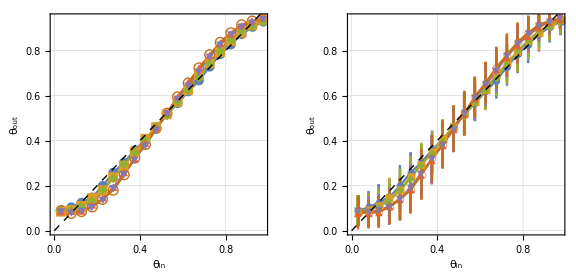

```mathematica
GraphicsRow[{Show[{ListLinePlot[meanscatter[[;;6]],AspectRatio->1,Frame->True,GridLines->Automatic,PlotMarkers->{Automatic, 10},FrameLabel->{"θ_in","θ_out"}],Plot[x,{x,0,1},PlotStyle->{Black,Thick,Dashed}]}],Show[{ErrorListPlot[meanscatterdatwiderror[[;;6]],AspectRatio->1,Frame->True,GridLines->Automatic,Joined->True,FrameLabel->{"θ_in","θ_out"},PlotMarkers->{Automatic, 10}],Plot[x,{x,0,1},PlotStyle->{Black,Thick,Dashed}]}]},ImageSize->Large]
```

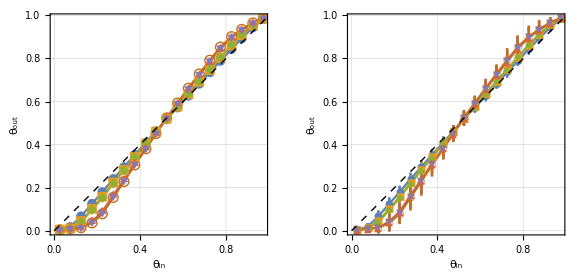

```mathematica
GraphicsRow[{Show[{ListLinePlot[meanscatter[[7;;]],AspectRatio->1,Frame->True,GridLines->Automatic,PlotMarkers->{Automatic, 10},FrameLabel->{"θ_in","θ_out"}],Plot[x,{x,0,1},PlotStyle->{Black,Thick,Dashed}]}],Show[{ErrorListPlot[meanscatterdatwiderror[[7;;]],AspectRatio->1,Frame->True,GridLines->Automatic,Joined->True,PlotMarkers->{Automatic, 10},FrameLabel->{"θ_in","θ_out"}],Plot[x,{x,0,1},PlotStyle->{Black,Thick,Dashed}]}]},ImageSize->Large]
```

comparison of various α at infinite persistence length. θ_in, θ_out in units rad/2.